# I Introduktion till Mathematica

KTH/ICT:IX1304 - Analys
Göran Andersson, goeran@kth.se ver. 130909
Senaste uppdatering: AD 29 augusti 2014

## Section Genomförande och bedömning

I den här projektuppgiften ingår introduktionsuppgifter till Mathematica och att lösa några matematiska problem, skriva en rapport i Mathematica om lösningsmetod och resultat, samt genomföra en kort muntlig presentation. Du ska arbeta i grupp tillsammans med en annan student.

Läs noga igenom denna instruktion samt informationen på kurshemsidan så att du vet vilka regler som gäller och vad som förväntas av dig.

Målen med projektuppgifterna är:
1. De ska underlätta inlärningen av kursinnehållet.
2. De ska träna matematiskt modellbyggande.
3. De ska ge träning i att tillverka och presentera rapporter.

## Section Förberedelser

### Section.Subsection Studier

Denna projektuppgift syftar till att du ska bekanta dig med Mathematica och lära dig elementär programmering i språket Mathematica.

Det är meningen att du ska använda Mathematica för att lösa uppgiften. Du behöver alltså inte ägna tid åt att försöka derivera och lösa ekvationer för hand. Du förutsätts ha kunskaper motsvarande  intoduktionsföreläsningen till Mathematica, plus övningen som hör till. Vi rekommenderar starkt att du studerar filen QuickIntro.nb, särskilt avsnitt 7 och 8. I QuickIntro.nb finns viktiga exempel på hur man använder de kommandon du behöver i denna övning. Det finns också en hel del korta filmsnuttar som förklarar grunderna. Se

www.wolfram.com/broadcast/screencasts/handsonstart/

Nedan följer några exempel på syntax som kan vara bra att känna till. Exekvera kommandona för att se resultaten.

### Section.Subsection Exakt eller inte?

I regel som gör Mathematica en exakt beräkning om alla indata är exakta.

```mathematica
2+5/7
```

Om däremot någon del av indata ges på flyttal (floating point number, inexakt form, numerisk form) så presenteras resultatet som ett flyttal.

```mathematica
2+5.0/7
```

Ett exakt resultat kan omvandlas till flyttal av godtycklig noggrannhet med N.

```mathematica
N[2+5/7]
```

```mathematica
N[2+5/7,50]
```

Lägg märke till det periodisk talet ovan som är en egenskap hos rationella tal. Normal räknar Mathematica flyttal med 16 siffror och presenterar resultat med sex sifftor. Om 5. anges istället för 5 så räknar Mathematica med 16 siffor och presenterar resultatet med 6 siffror även om vi begär utskrift med 50 siffror.

```mathematica
N[2+5./7,50]
```

Vi kan dock ange n siffrors precision med 5.`n. Resultatet presenteras med den precision som är lägst:

```mathematica
2+5.0`30/7.`50  (* 30 siffrors precision i resultatet *)
```

Man bör använda högre precision (t.ex. + 10 siffror) i ingående tal än i resultatet. Sålunda kan vi lämpligen presentera föregående resultat med 20 siffror.

```mathematica
SetPrecision[2+5.0`30/7.`50,20]
```

Det finns i vissa fall metoder som är speciella beroende på om man vill ha exakt eller numerisk behandling. I dessa fall börjar de numeriska metoderna med N. Exempelvis

Solve		—	NSolve
Integrate	—	NIntegrate
Sum			—	NSum
Minimize	—	NMinimize
⋮				⋮

Om ingen exaktlösning är NIntegrate att föredra istället för N[Integrate]. Exempelvis:

```mathematica
NIntegrate[Sin[x]/x,{x,0,10}] (* ingen exakt beräkning *)
```

```mathematica
N[Integrate[Sin[x]/x,{x,0,10}]] (* först exakt och sedan numerisk beräkning *)
```

### Section.Subsection Definition av funktion

#### Section.Subsection.Subsubsection Enkel metod

```mathematica
ClearAll["`*"]
```

Vid tilldelning av data används normalt Set (=) i Mathematica. Vilket innebär att högerledet evalueras.

```mathematica
x=Cos[π/3]+Sin[π/3]
```

x tilldelas alltså resultatet av evalueringen av högerledet.

```mathematica
?x
```

Vid definition av en funktion (metod) vill man oftast att högerledet ska betraktas som en kod som inte ska evalueras. Då används SetDelayed (:=). Här följer ett exempel f(x)=x^3-3x+1

```mathematica
f[x_]:=x^3-3x+1
```

Ingen evaluering sker vilket vi inte vill här eftersom ju x har ett värde. Mönstret (the pattern) i vänsterledet accepterar nu, på grund av _ eller Blank, alla uttryck av typ f[anything].

```mathematica
MatchQ[Hold[f[anything]],Hold[f[x_]]]
```

```mathematica
MatchQ[Hold[f[17]],Hold[f[x_]]]
```

Det innebär att vi kan använda f som en vanlig funktion. I högerledet kommer anything att temporärt tilldelas symbolen x och sedan sker evalueraing.

```mathematica
f[anything]
```

```mathematica
f[17]
```

```mathematica
f[x] (* observera att x har tilldelats ovan *)
```

```mathematica
f[1+t]
```

```mathematica
Plot[f[x],{x,-2,2},AxesLabel->{"x","f[x]"}]
```

Vi har bara definierat vår funktion för ett indata. Det gör att funktionen inte reagerar för fler indata.

```mathematica
f[a,b]
```

```mathematica
MatchQ[Hold[f[a,b]],Hold[f[x_]]]
```

Eftersom Mathematica använder overloading är det emellertid inga problem att utvidga vär funktion till fler variabler:

```mathematica
f[x_,y_]:=x^3-3y+1
```

```mathematica
Manipulate[
Plot[
f[x,y],{x,-2,2},
PlotRange->{-20,20},AxesLabel->{"x",StringForm["f[x,`1`]",y]}
],
{y,-5,5}]
```

#### Section.Subsection.Subsubsection Metod med lokala variabler

Vi programering av mer avancerade metoder är koden ofta ett litet program med lokala variabler. Detta åstadkommes med Module i Mathematica. Syntaxen är (observera komma och semikolon):

Module[
 {a, b, c}, (* list with local variables *)
 statement1;
 statement2;
 ⋮
 statementlast
 ]

Antag att vi vill skapa en metod som räknar ut moms. För en producent är momsen 25%, dvs. om du har räknat fram att varan ska kosta 100 kr för att din ekonomi ska bli acceptabel så ska kunden betala 125 kr eftersom staten tar 25 kr. Här är en metod som använder Module och som räknar ut butikspriset (bruttopriset).

```mathematica
bruttospris[nettopris_,momssats_]:=Module[
{moms},
moms=nettopris*momssats;
nettopris+moms
]
```

```mathematica
butikspris[100,0.25]
```

Som kund är du istället intresserad av att veta vilken skatt som ingår i butikspriset.

```mathematica
skatt[bruttopris_,momssats_]:=Module[
{m},
m=momssats/(1+momssats);
bruttopris*m
]
```

```mathematica
skatt[125,0.25]
```

#### Section.Subsection.Subsubsection En mer generell metod

Varning: Koden nedan är mer avancerad än vad som krävs för projektet och kan verka förvirrande för en nybörjare. Den kan också ge upphov till nya tankebanor.

Du har säker lagt märke tiil att man kan använda Options i Plot för att sätta etiketter på axlarna och ange färg på kurvan etc. Vi ska nu generalisera vår skatt metod så att momssatsen läggs in som option. Vidare lägger vi in en option som avgör om vi är konsument eller producent (näringsidkare).

```mathematica
Clear[skatt]
```

Vi börjar med att definiera default-värden för optionerna:

```mathematica
Options[skatt]={momssats->0.25,typ->"konsument"};
```

Nästa steg blir att definiera help-information:

```mathematica
skatt::usage="skatt[belopp] returnerar momsbeloppet";
momssats::usage="option för skatt som bestämmer momssatsen";
typ::usage="option för skatt som bestämmer om momsen ska beräknas för \"konsument\" eller \"producent\"";
```

Vi forsätter med ett par felmeddelanden:

```mathematica
skatt::moms="momssatsen ska positiv";
skatt::typ="felaktig typ (`1`)";
```

Här följer nu koden för vår nya skatt-metod:

```mathematica
skatt[belopp_, OptionsPattern[]]:=Module[
{m,t},
m=OptionValue[momssats];
t=OptionValue[typ];
If[!NumericQ[m],Return[Message[skatt::moms]]];
If[!Positive[m],Return[Message[skatt::moms]]];
If[!StringQ[t],Return[Message[skatt::typ,Head[t]]]];
If[!StringMatchQ[t,"konsument"|"producent",IgnoreCase->True],Return[Message[skatt::typ,t]]];
If[StringMatchQ[t,"producent",IgnoreCase->True],
m*belopp,m/(1+m)*belopp]
]
```

OptionsPattern är ett mönster som filtrerar de optioner som är givna för metoden. Det är därmed möjligt att ange 0 eller flera optioner.

```mathematica
skatt[125]   (* ingående moms *)
```

```mathematica
skatt[100,typ->"producent"]  (* påslagsmoms *)
```

```mathematica
skatt[100,typ->"producent",momssats->0.06]
```

Om vi vill att producent ska vara default kan vi ange detta med

```mathematica
SetOptions[skatt,typ->"producent"]
```

```mathematica
skatt[100] (* påslagsmoms *)
```

Låt oss testa information och felmeddelanden:

```mathematica
?skatt
```

```mathematica
skatt[100,momssats->-0.2]
```

```mathematica
skatt[100,typ->producent]
```

```mathematica
skatt[100,typ->"prod"]
```

```mathematica
?typ
```

### Section.Subsection Lösning av ekvationer

#### Section.Subsection.Subsubsection Exakt lösning

Algebraiska ekvationer och vissa andra ekvationer kan lösas exakt med Solve i Mathematica. Ett exempel visar den grundläggande syntaxen.

```mathematica
ClearAll["`*"]
```

```mathematica
equation=3 x^2+4x==5;
solution=Solve[equation,x]
```

Observera att lösningen ges i form av regler (→ Rule) som kan användas till substitution (/. ReplaceAll). Om vi vill tilldela lösningarna till x1 respektive x2 används

```mathematica
{x1,x2}=x/.solution
```

Ett numeriskt värde kan erhållas med N.

Eftersom lösningarna x1 och x2 nu är tilldelade kan värdena användas:

```mathematica
y=x1+x2//Simplify
```

Om det bara finns en lösning följer syntaxen samma idé som ovan:

```mathematica
{x1}=x/.Solve[3x+4==5,x]
```

```mathematica
x1
```

Han man flera ekvationer skrivs de in i en lista {}.

```mathematica
Clear[x,y];
solution=Solve[{x^2-y^2==1,x+2y==3},{x,y}]
```

Tilldelningen sker enligt:

```mathematica
{{x1,y1},{x2,y2}}={x,y}/.solution
```

Här är en graf som visar de två lösningspunkterna:

```mathematica
ContourPlot[{x^2-y^2==1,x+2y==3},{x,-5,5},{y,-5,5},Epilog->{PointSize[0.015],Point[{x1,y1}],Point[{x2,y2}]},FrameLabel->{x,y}]
```

En mer generell ekvationslösning erhålls med Reduce.

#### Section.Subsection.Subsubsection Numerisk lösning

```mathematica
ClearAll["`*"]
```

Om ekvationerna är algebraiska kan man använda NSolve enligt syntaxen föregående sektion.

```mathematica
equation=3 x^2+4x==5;
{x1,x2}=x/.NSolve[equation,x]
```

```mathematica
x1+x2
```

Metoden FindRoot kan användas på alla typer av ekvationer, men man måste ange ett startvärde för lösningen (Newton-Raphsons metod). Antag att vi vill lösa ekvationen cos(x)-x=0. Eftersom vi vill ha ett startvärde så vi börjar med en plot.

```mathematica
Plot[Cos[x]-x,{x,0,1},AxesLabel->Automatic]
```

Av grafen framgår att x_0=0.75 är ett bra startvärde.

```mathematica
equation=Cos[x]-x==0;
x0=0.75;
solution=FindRoot[equation,{x,x0}]
```

Observera att lösningen ges med bara en listnivå här. Därför skrivs inte {x1} = x/.solution vid tilldelningen.

```mathematica
x1=x/.solution
```

Han man flera ekvationer skrivs de in i en lista {}.

```mathematica
Clear[x,y];
curvePlot=ContourPlot[{2x+y==Cos[x],x+2y==1},{x,-2,2},{y,-1,3},FrameLabel->{x,y},GridLines->Automatic]
```

Vi kan se att (x_0,y_0)=(0.4,0.4) är en någorlunda bra startpunkt.

```mathematica
{x0,y0}={0.4,0.4};
solution=FindRoot[{2x+y==Cos[x],x+2y==1},{{x,x0},{y,y0}}]
```

Tilldelningen sker enligt:

```mathematica
{x1,y1}={x,y}/.solution
```

Här är en graf som visar lösningspunkten:

```mathematica
solutionPoint=Graphics[{PointSize[0.015],Point[{x1,y1}]}];
Show[curvePlot,solutionPoint]
```

#### Section.Subsection.Subsubsection Reella lösningar

Mathematica arbetar ofta med komplexa tal som definitionsmängd (default). I många fall är man vid ekvationslösning endast intresserad av lösningar som (exempelvis) rella eller heltal. Det kan då vara intressant att begränsa lösningsmängden. Här följer ett par exempel:

Vi börjar med att studera f(x)=x^3-(3 x)/2-(3 √3)/2.

```mathematica
ClearAll["`*"]
```

```mathematica
f[x_]:=x^3-(3 x)/2-(3 √3)/2
```

```mathematica
Plot[f[x],{x,-2,3},AxesLabel->{"x","f"}]
```

Som framgår av grafen så finns ett nollställe x≈1.7. Vi kan söka detta med

```mathematica
FindRoot[f[x]==0,{x,1.7}]
```

Vi kan få ett exakt värde med Solve. För att undvika komplexa lösningar kan definitionsmängden anges till reella tal.

```mathematica
Solve[f[x]==0,x,Reals]
```

I många fall är ett exaktvärde så komplicerat att det exakta uttrycket är ointressant. Då ges endast en exakt representation av roten med Root. T.ex.

```mathematica
g[x_]:=x^5+x+1;
{x0}=x/.Solve[g[x]==0,x,Reals]
```

Vi kan ändå se att lösningen är exakt:

```mathematica
Simplify[g[x0]]
```

Just i detta fall är faktiskt lösningen inte så komplicerad och vi kan forcera fram ett rotuttryck:

```mathematica
ToRadicals[x0]
```

I vissa fall är man bara intresserad av heltalslösningar. T.ex.

```mathematica
solution=Solve[{13x+17y==1000,x>0,y>0},Integers]
```

```mathematica
{x,y}/.solution
```

Vi får alltså fem lösningar om heltalen x och y ska vara positiva. Nedan visas syntaxen med Reduce som är ett mer avancerat kommando än Solve:

```mathematica
solution=Reduce[13 x+17 y==1000&&x>0&&y>0,Integers]
```

Vi kan se att svaret ges i en annorlunda form. Om lösningen är utan villokor kan den omvandlas på samma form som i fallet Solve med

```mathematica
{ToRules[solution]}
```

### Section.Subsection Derivata

#### Section.Subsection.Subsubsection Derivata i Mathematica

```mathematica
ClearAll["`*"]
```

Det finns många sätt att derivera i Mathematica. Här visas de viktigaste. Den enlaste metoden är att definiera en funktion f[x] och ange f’[x] för derivatan f’’[x] för andra derivatan etc. Fördelen med denna syntax är att man kan ange värden på x på ett enkelt sätt, t.ex. f’[3].

f'[x], f''[x], f'''[x], etc...

Exempel:

```mathematica
f[x_]:=ⅇ^-x Sin[x]
```

```mathematica
f'[x]
```

```mathematica
f''[π]
```

Om man vill ange t.ex. d^15 f/d x^15 är föregående syntax något klumpig. Man kan då använda D.

D[f, x], D[f, {x, 2}], D[f, {x, 3}],...

```mathematica
D[f[x],{x,15}]
```

Denna syntax tillåter inte insättning av värden direkt eftersom t.ex. D[f[π/2],x] tolkas som derivata av f(π/2)=e^(-π/2) som ju är 0. Ett alternativ är då substitution:

```mathematica
D[f[x],{x,15}]/.{x->π/2}
```

Ytterligare en möjlighet är den mer avancerade syntaxen Derivative som tillåter insättning.

```mathematica
Derivative[15][f][π/2]
```

Derivative[1][g] är egentligen den fullständiga syntaxen för g’.

```mathematica
Derivative[1][g][x]
```

#### Section.Subsection.Subsubsection Ett optimeringsproblem

Detta problem är hämtat från ett exempel i läoboken.

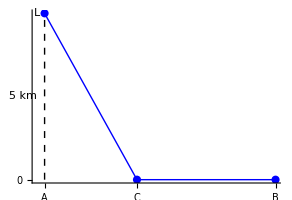

A lighthouse is L is located on a small island 5km north of a point A on the straight east-west shoreline. A cable is to be laid from L to point B on the shoreline 10km east of A. The cable will be laid through the water in a straight line from L to a point C on the shoreline between A and B and from there to B along the shoreline. The part of cable lying in the water costs $5500/km, and the part along the shoreline costs $3000/km. Where should C be chosen to minimize the total cost of the cable?

```mathematica
ClearAll["`*"]
```

Vi inför avståndet AC som x.

```mathematica
AC=x;AL=5;
LC=√(AL^2+AC^2)
```

```mathematica
CB=10-AC
```

Vi ska nu minimera kostnaden för kabeldragningen. Det kostar $5500/km längs LC och $3000 längs CB. Kostnaden c(x) blir därmed

```mathematica
c[x_]=5500LC+3000CB
```

```mathematica
Plot[c[x],{x,0,10},AxesLabel->{"x [km]","cost [$]"}]
```

Observera att skala och positionen av origo ofta är avgörande för hur man uppfattar informationen. Se PlotRange, AxesOrigin och AspectRatio. I ovanstående plot verkar positionen av C vara extremt viktig för kostnaden. Om vi tar med $0 blir bilden en annan:

```mathematica
Plot[c[x],{x,0,10},AxesLabel->{"x [km]","cost [$]"},PlotRange->{0,All}]
```

Vi söker nu derivatans nollställen:

```mathematica
c'[x]
```

```mathematica
solution=Solve[c'[x]==0,x]
```

```mathematica
{x0}=x/.solution
```

```mathematica
N[x0]
```

Den minsta kostnaden är nu finns nu i någon punkt där derivatan är 0 eller i ändpunkterna, dvs. vi söker min(c(0),c(x_0),c(10))

```mathematica
cmin=Min[{c[0],c[x0],c[10]}]
```

```mathematica
N[cmin]
```

Kabeln ska alltså dras i havet från L till C vid x≈3.25km väster om öster om A och sedan på land mot B. Kostnaden blir drygt $53000.

### Section.Subsection Integral

#### Section.Subsection.Subsubsection Integral i Mathematica

```mathematica
ClearAll["`*"]
```

En primitiv funktion beräknas med

Integrate[f[x], x]

Exempel:

```mathematica
f[x_]:=x ⅇ^-x
```

```mathematica
Integrate[f[x],x]
```

En integral har samma syntax, men man anger integrationsgränser:

Integrate[f[x], {x, a, b}]
NIntegrate[f[x], {x, a, b}]

```mathematica
Integrate[f[x],{x,1,2}]
```

```mathematica
NIntegrate[f[x],{x,1,2}]
```

#### Section.Subsection.Subsubsection Beräkning av en area

Detta problem liknar ett exempel i läoboken.

Find the area below y=9/(x^4+4 x^2+3) and above y=1.

Vi börjar med en numerisk beräkning

```mathematica
ClearAll["`*"]
```

```mathematica
ContourPlot[{y==9/(x^4+4 x^2+3),y==1},{x,-3,3},{y,-2,4},FrameLabel->{x,y},GridLines->Automatic]
```

Vi börjar med att söka skärningspunkterna

```mathematica
x0=x/.FindRoot[9/(x^4+4 x^2+3)==1,{x,-1}]
```

```mathematica
x1=x/.FindRoot[9/(x^4+4 x^2+3)==1,{x,1}]
```

Den inneslutna arean kan nu beräkna enligt

```mathematica
area=NIntegrate[9/(x^4+4 x^2+3)-1,{x,x0,x1}]
```

Här är en bild av den inneslutna ytan:

```mathematica
plot1=Plot[{9/(x^4+4 x^2+3),1},{x,-3,3},AxesLabel->{x,y}];plot2=Plot[{9/(x^4+4 x^2+3),1},{x,x0,x1},Filling->{1->{2}}];
Show[plot1,plot2]
```

Här följer en exakt beräkning:

Vi börjar med att söka skärningspunkterna

```mathematica
𝕩=x/.Solve[9/(x^4+4 x^2+3)==1,Reals]//ToRadicals
```

Den exakta arean kan nu beräkna med

```mathematica
exactArea=Integrate[9/(x^4+4 x^2+3)-1,{x,𝕩⟦1⟧,𝕩⟦2⟧}]
```

```mathematica
TraditionalForm[exactArea]
```

```mathematica
N[exactArea]
```

## Section Matematiska problem

### Section.Subsection Undersökning av en funktion

#### a)

Definiera funktionen

f(x)=x^3-ax^2+x+1 

Sätt a till födelsedagen för en av gruppmedlemmarna (dvs ett tal mellan 1 och 31). Plotta funktionen i lämpligt intervall. Glöm inte etiketter på axlarna.

```mathematica
Clear[f]
f[x_] :=x^3-15 x^2+x+1
```

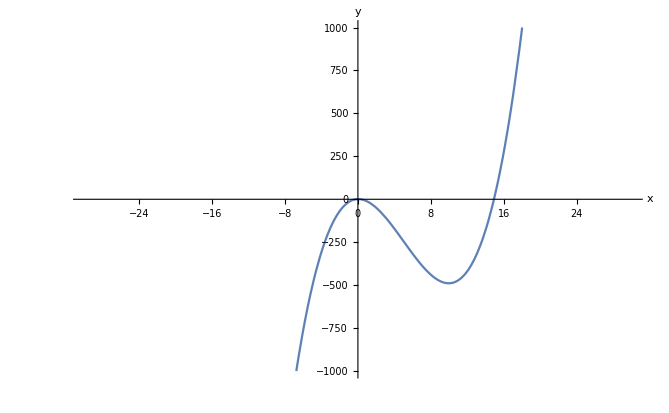

```mathematica
Plot[f[x] , {x,-30,30},AxesLabel->{x,y}, PlotRange->{-1000,1000}]
```

#### b)

Bestäm exakt funktionens nollställen. Hur många nollställen hittar Mathematica? Hur många nollställen kan maximalt finnas? Markera dessa nollställen med röda punkter i grafen i a).

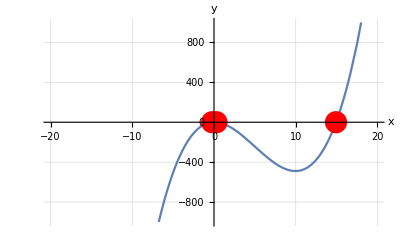

5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3)

5-((1+ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1-ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3)

5-((1+ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1-ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)

```mathematica
Plot[f[x], {x,-20,20},AxesLabel->{"x","y"},PlotRange->{-1000,1000},LabelStyle->(FontSize->16),GridLines ->Automatic,Epilog->{Red,PointSize[0.04], Point[{x1,0}], Point[{x2,0}], Point[{x3,0}]}]

{x1,x2,x3}=x/.Solve[f[x]==0,x];
x1
x2
x3
```

#### c)

Bestäm funktionens derivata och repetera a) och b) för derivatan.

```mathematica
ClearAll["Global`*"]
```

```mathematica
f[x_]:= x^3-15 x^2+x+1
```

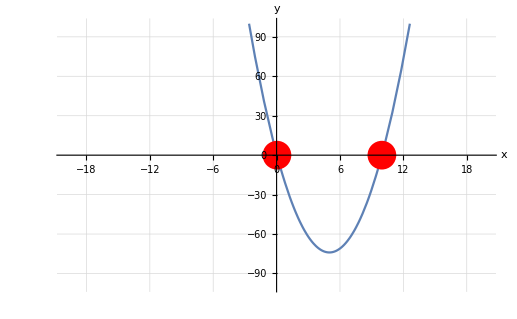

1/3 (15-√222)

1/3 (15+√222)

```mathematica
Plot[f'[x],{x,-20,20},AxesLabel->{"x","y"},PlotRange->{-100,100},LabelStyle->(FontSize->16),GridLines ->Automatic,Epilog->{Red,PointSize[0.04], Point[{x1,0}], Point[{x2,0}]}]

{x1,x2}=x/.Solve[f'[x]==0,x];
x1
x2
```

#### d)

Plotta f(x) i intervallet [x_1,x_3], där x_1 är det minsta av funktionens nollställen och x_3 är det största. Bestäm funktionens maxvärde i detta intervall. Du bör ha fått reda på vilket värde på x du ska använda i c).

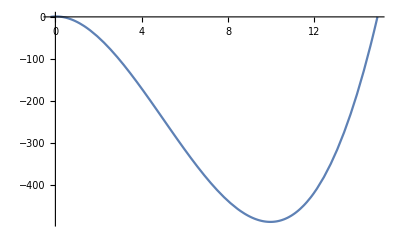

```mathematica
Plot[x^3-15 x^2+x+1,{x,5+(2 (549+ⅈ √2517))^(1/3)/3^(2/3)+(37 2^(2/3))/(3 (549+ⅈ √2517))^(1/3),5-((1-ⅈ √3) (549+ⅈ √2517)^(1/3))/6^(2/3)-(37 (1+ⅈ √3))/(6 (549+ⅈ √2517))^(1/3)}]
```

```mathematica
Last[FindMaximum[x^3-15 x^2+x+1,{x,0,15}]]
```

{x→0.0334452}

```mathematica
x->0.033445191402866316
```

x→0.0334452

```mathematica
Solve[Y==0.033445191402866316^3-150*(.033445191402866316`)^2+0.033445191402866316`+1]
```

{{Y→-0.134305}}

### Section.Subsection Beräkning av en area

#### a)

Plotta funktionerna

f(x)=2/(1+ax^2) och g(x)=1/(√(1+ax^2))

i lämpligt  intervall. Sätt värdet på a till samma som i uppgift 1. För a=1 är ett bra plottningsintervall x=[0,3]. Se till att det finns etiketter på axlarna, att båda kurvornas skärningpunkter med y-axeln finns med, att skärningspunkten mellan kurvorna finns med, samt att origo finns med i plotten.

```mathematica
f[x_] :=2/(1+15 x^2)
g[x_] :=1/(Sqrt[1+15x^2])
```

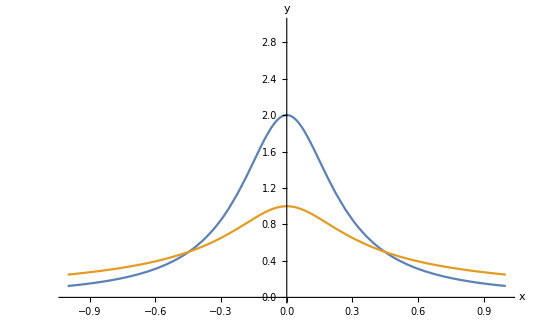

```mathematica
Plot[{f[x],g[x]},{x,-1,1},AxesLabel->{"x","y"},PlotRange-> {0,3}]
```

#### b)

Du kan se att funktionerna skär varandra i en punkt (x_1,y_1). Bestäm denna punkt exakt.

```mathematica
x/.Solve[f[x]==g[x],x]
```

{-1/(√5),1/(√5)}

```mathematica
Subscript[y, 1]==2/(1+15((1/(√5))^2))
Subscript[y, 1]==1/((1+15(1/(√5))^2)^(1/2))
```

y_1==1/2

y_1==1/2

```mathematica
Svar:(Subscript[x, 1],Subscript[y, 1])==(1/(√5),1/2)
```

#### c)

Från gymnasieskolan känner du säkert till att arean under grafen till en funktion kan beräknas med en integral.

A=∫_a^b f(x)dx

Bestäm den area som finns mellan funktionerna i intervallet [0,x_1]. Du kan beräkna den som skillnaden mellan två areor. Du behöver inte bestämma arean exakt utan det går bra att använda NIntegrate.

```mathematica
A==NIntegrate[(f[x]),{x,0,1/(√5)}]-NIntegrate[(g[x]),{x,0,1/(√5)}]
```

A==0.200733

```mathematica
A==Svar
```

### Section.Subsection Ett problem från ellära

Elgeneratorer (t ex vattenturbiner) ger ofta en sinusformad spänning. I den här uppgiften undersöker vi vad som händer om man seriekopplar två sådana elgeneratorer. Figuren nedan illustrerar situationen.
-Graphics-

Vi har alltså två generatorer. Den ena ger en spänning med amplitud A_1och fas ϕ_1, den andra ger en spänning med amplitud A_2 och fas ϕ_2. Båda har samma frekvens υ = 50 Hz.  ω står för vinkelfrekvensen, vilket är 2πυ.

#### a)

Plotta y_1 och  y_2 i intervallet t = 0 till 5T, där T = perioden = 2π/ω = 1/υ. Plotta för flera olika värden på amplituderna och faserna. Läs gärna igenom uppgift b och c innan du börjar så att du kan välja samt plotta kombinationer av värden på amplituder och faser på ett genomtänkt sätt. Hur många maxima hittar du i intervallet t=[0, 5T]? Vad är enheten för fasvinklarna ϕ_1 och ϕ_2?

```mathematica
ClearAll["Global`*"]
```

```mathematica
A1 :=1
```

```mathematica
A2 :=2

Upsilon :=50
Omega:=2Pi*Upsilon
T :=1/Upsilon
phi1 := Pi/3
phi2 := Pi/6
```

```mathematica
Y1[t_]:=A1*Sin [Omega*t+phi1]
```

```mathematica
Y2[t_]:=A2*Sin[Omega*t+phi2]
```

2 sin[100 π t+ϕ1]

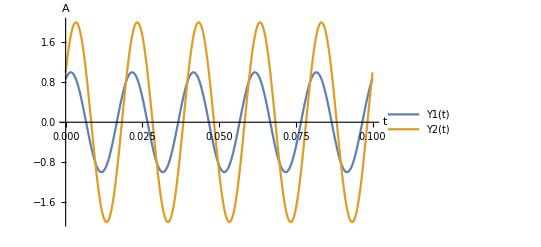

```mathematica
Plot[{Y1[t],Y2[t]},{t,0,5T}, PlotLegends->"Expressions", AxesLabel->{"t","A"}]
```

```mathematica
(*5 maximi och 5 mini på båda
Enheten för faserna är radiarner*)
```

#### b)

Plotta nu även summan av y_1 och  y_2 för de värden du valde ovan. Diskutera kvalitativt hur amplituden och fasen för summan verkar bero av amplituderna och faserna hos y_1 och  y_2.

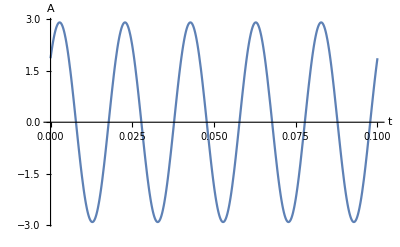

```mathematica
Plot[(Y1[t]+Y2[t]),{t,0,5T},AxesLabel->{"t","A"}]
```

```mathematica
(*Apmlituden av första och adnra funktionen adderas i summan*)
(*Saumman fas blir likadan som i Y1s fas*)
```

#### c)

Byt nu ena frekvensen till 60 Hz, dvs våra generatorer har nu lite olika frekvens. Diskutera kvalitativt hur summan av y_1 och  y_2 påverkas av detta. Verkar det bra eller dåligt att seriekoppla turbiner med olika frekvens?

```mathematica
Upsilon2 :=60
```

```mathematica
Omega2:=2Pi*Upsilon2
```

```mathematica
Y3[t_] := A1*Sin [Omega2*t+phi1]
```

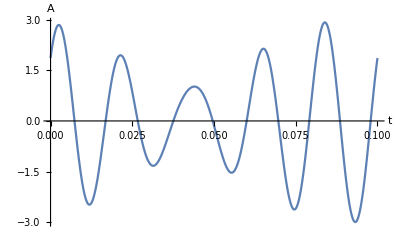

```mathematica
Plot[(Y2[t]+Y3[t]),{t,0,5T},AxesLabel->{"t","A"}]
```

```mathematica
(*Nej, det verkar inte vara bra att seriekopla två turbiner med olika frekvens eftrsom det sker obalans mellan turbinerna*)
```